# The Walking Dead : Malaria Edition

## Functions

```mathematica
SetDirectory[NotebookDirectory[]]
(*Movement Kernels*)
CalculateEuclideanDistances[coordinatesSet_]:=Table[N[EuclideanDistance[coordinatesSet[[i]],#]]&/@coordinatesSet,{i,1,coordinatesSet//Length }]
(* This one is out of date; use the exponential one instead:
CalculateInverseLinearKernelMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce] *)
ExponentialKernel[λ_,distance_]:=λ*ⅇ^(-λ*distance)
(*Markov - Calculates fraction of time mosquitoes spend at each network node, given a Markov process
migrationProbabilities = transitions probability matrix, calculated using Euclidean distances and a Kernel *)
CalculateMarkovSteadyState[migrationProbabilities_]:=Module[{initialState,markov,markovPDF},
initialState=ConstantArray[0,migrationProbabilities//Length]//ReplacePart[#,1->1]&;
markov=DiscreteMarkovProcess[initialState,migrationProbabilities];
markovPDF=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length];
markovPDF
]
(*Networks Plot*)
edgeshape[e_,___]:={Arrowheads[{{.0075,.5}}],Arrow[e]}
Options[EdgesStyleList]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],
"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[1*vertexSyllableList[[i]][[2]]+.025],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.75*vertexSyllableList[[i]][[2]]+.05],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
VertexNumberToVertexSyllable[syllables_,fixedEdgesList_]:=Table[DirectedEdge[syllables[[fixedEdgesList[[index]][[1]][[1]]]],syllables[[fixedEdgesList[[index]][[1]][[2]]]]->fixedEdgesList[[index]][[2]]]//N,{index,1,Length[fixedEdgesList]}]
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,PlotTheme->"LakeNetwork",EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
(*Plots Styles*)
Themes`AddThemeRules["LakeMatrixPlot"
,AspectRatio->1
,AxesStyle->Directive[Gray,Opacity[.5],Dashed]
,ColorFunction->ColorData[{"LakeColors","Reverse"}]
,Frame->True
,FrameStyle->Directive[Gray,Thick]
,FrameTicks->False
,ImageSize->250
,PlotRangePadding->0
]
Themes`AddThemeRules["LakeNetwork",
,EdgeShapeFunction->edgeshape2
,Epilog->Riffle[ConstantArray[Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]],sampledCoordinates//Length],(Disk[#,.25]&/@sampledCoordinates)]
,ImageSize -> 500
,ImagePadding->25
,LineThickness -> .0075
,VariableStyle->"Both"
,VertexCoordinates ->sampledCoordinates
,VertexSize ->.01
,VertexLabelStyle->.001
]
(*USES GLOBALS!*)
GraphPlotWrapper[migrationMatrix_,max_,vertexSize_,vertexStyle_]:= GraphTransitionsFrequenciesWithMax[
  {
migrationMatrix,
ToString /@ Range[Length[migrationMatrix]]
   }, max
,EdgeShapeFunction->edgeshape2
,ImagePadding->0
,ImageSize->imageSize
,LineThickness->lineThickness
,VariableStyle->"Both"
,VertexCoordinates->sampledCoordinates
,VertexSize -> vertexSize
,VertexStyle->vertexStyle
,VertexLabelStyle->.0001
  ]
```

/Users/dtcitron/Documents/MosPopDyn/MoNeT/MoNeT/Dev/DanielCitron

LakeMatrixPlot

LakeNetwork

## Inputs

Style

```mathematica
edgeChopThreshold=10^-1.5;
edgeshape2[e_,___]:={Arrowheads[{{.000000001,1}}],Arrow[e]}
lineThickness=.0005;
imageSize=250;
```

Geo - Setting

```mathematica
(* Define:
citiesNumber - {size of grid, distance between cities}, used as a way of defining all the different cities;
 networkDimension - number of node types;
 distance - distance between cities;
*)
{citiesNumber,networkDimension,distance}={{100,50},2,50};
(**)
movementProbabilitiesVector=If[networkDimension>1,ConstantArray[0,networkDimension]//ReplacePart[#,{2->1,3->0}]&,ConstantArray[0,networkDimension]//ReplacePart[#,{1->1}]&];
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,networkDimension}];
MatrixForm[penalizationsMatrix]
```

(0 | 1
1 | 0)

Random Walks

```mathematica
{chainsSteps,chainsNumber}={20,30};
```

## Spatial Setting

2 D - Grid

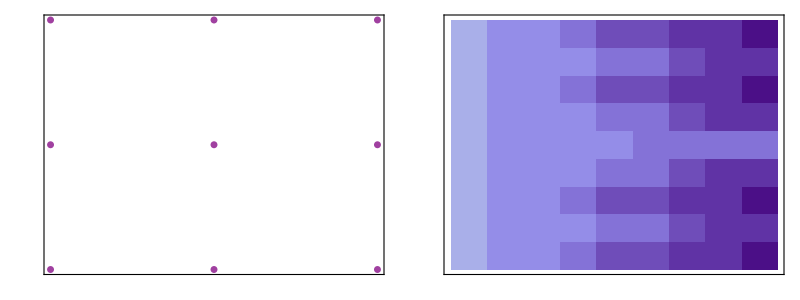

```mathematica
citiesSqrt=Range[0,citiesNumber[[1]],citiesNumber[[2]]];
sampledCoordinates=Tuples[citiesSqrt,2];
clusteredCoordinates=FindClusters[sampledCoordinates,Method->"NeighborhoodContraction"];
euclideanDistances=CalculateEuclideanDistances[sampledCoordinates];
(**)
colors=Reverse[ColorData["BrightBands",#]&/@Range[0,1,1/(Length[clusteredCoordinates])]]//Flatten//RandomSample;
gridCoordinatesPlot=ListPlot[clusteredCoordinates//Flatten[#,1]&
,AspectRatio->1
,AxesStyle->Directive[Gray,Opacity[.5],Dashed]
,GridLines->None
,GridLinesStyle->Directive[Gray,Opacity[.5],Dashed]
,ImageSize->250
,PlotRangePadding->.5
,PlotStyle->Directive[Purple,EdgeStyle[Black],Opacity[.75],PointSize[.02]]
,Frame->True
,FrameStyle->Directive[Gray,Thick]
,FrameTicks->False
,FrameTicksStyle->15
];
matrixDistancesPlot=MatrixPlot[Sort/@euclideanDistances,PlotTheme->"LakeMatrixPlot"];
Grid[{{gridCoordinatesPlot,matrixDistancesPlot}}]
```

Movement Kernel

### Inverse-Linear Kernel

```mathematica
(*migrationProbabilities=CalculateInverseLinearKernelMigrationProbabilities[euclideanDistances,0];
(**)
matrixMigrationPlot=MatrixPlot[Sort/@migrationProbabilities,PlotTheme->"LakeMatrixPlot"];
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#]->stylesSwatchType[[1]])&/@Range[migrationProbabilities//Length];
originalMap=GraphPlotWrapper[
Chop[migrationProbabilities//LowerTriangularize,edgeChopThreshold],.1,
(#->.5)&/@(ToString/@Range[migrationProbabilities//Length]),
stylesListType
];*)
```

### Exponential Kernel

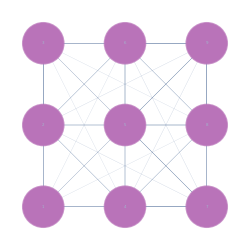

```mathematica
migrationProbabilities=(#/Total[#])&/@ReplacePart[ExponentialKernel[0.01848777,#]&/@euclideanDistances,{i_,i_}->0];
(**)
matrixMigrationPlot=MatrixPlot[Sort/@migrationProbabilities,PlotTheme->"LakeMatrixPlot"];
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#]->stylesSwatchType[[1]])&/@Range[migrationProbabilities//Length];
originalMap=GraphPlotWrapper[
Chop[migrationProbabilities//LowerTriangularize,.05*edgeChopThreshold],.1,
(#->.5)&/@(ToString/@Range[migrationProbabilities//Length]),
stylesListType
]
```

Markov Baseline

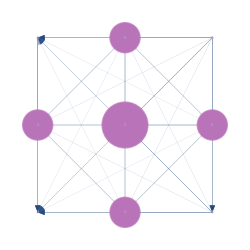

```mathematica
baselineMarkovSS=CalculateMarkovSteadyState[migrationProbabilities];
(**)
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#]->stylesSwatchType[[1]])&/@Range[migrationProbabilities//Length];
markovBaseline=GraphPlotWrapper[
Chop[migrationProbabilities//LowerTriangularize,.05*edgeChopThreshold],.1,
Thread[VertexList[originalMap ]->.25*Log[.5+7.5*Rescale[baselineMarkovSS]]],
stylesListType
]
```

## Network Dimensionality

Dimension

{1,2,1,1,2,2,2,1,2}

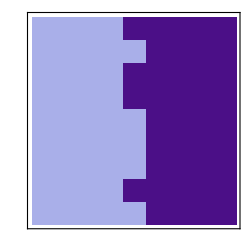

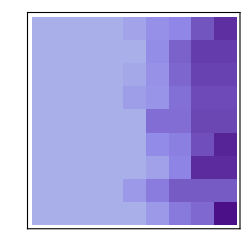

```mathematica
cityType={1,2,1,1,2,2,2,1,2} (*RandomChoice[Range[networkDimension],sampledCoordinates//Length]*)
dimensionalPenalizationsMask=Table[penalizationsMatrix[[i,#]]&/@cityType,{i,cityType}]; (* Very elegant way of generating full matrix of how we're re-weighting all edges according to  *)
migrationDimensionalMatrix=(#/Total[#])&/@(dimensionalPenalizationsMask*migrationProbabilities);
(**)
matrixPenalizationsPlot=MatrixPlot[Sort/@dimensionalPenalizationsMask,PlotTheme->"LakeMatrixPlot"]
matrixDimensionalPlot=MatrixPlot[Sort/@migrationDimensionalMatrix,PlotTheme->"LakeMatrixPlot"]
```

Markov Dimensional Network

```mathematica
(* Here we are plotting the following:
1. All of the nodes ;
  2. Which type each node is (node color);
  3. How frequently each node is visited, ie the markov steady state (node size);
  4. How frequently transitions are made, and which edges are allowed (edge width);
  *)
```

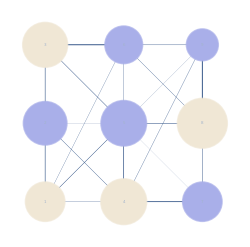

```mathematica
markovPDF=CalculateMarkovSteadyState[migrationDimensionalMatrix];
(**)
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
markovDimensional=GraphPlotWrapper[
Chop[migrationDimensionalMatrix//LowerTriangularize,edgeChopThreshold],.1,
Thread[VertexList[originalMap ]->.25*Log[5+7.5*Rescale[markovPDF]]],
stylesListType
]
```

Markov Dimensional Difference

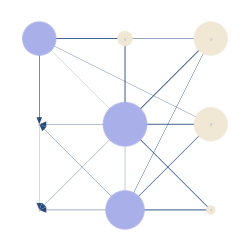

```mathematica
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
markovDimensionalDifference=GraphPlotWrapper[
Chop[migrationDimensionalMatrix//LowerTriangularize,edgeChopThreshold],.1,
Thread[VertexList[originalMap ]->.25*Log[0+7.5*Rescale[Chop[Abs[baselineMarkovSS-markovPDF]]]]],
stylesListType
]
```

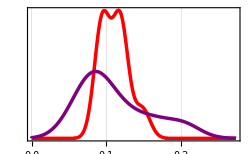

```mathematica
distributionOfDifferences=DistributionChart[baselineMarkovSS-markovPDF
,AspectRatio->1/6
,Axes->{False,True}
,AxesOrigin->{0,0}
,AxesStyle->Directive[Thick,Gray,Opacity[.25]]
,BarOrigin->Right
,BarSpacing->0
,ChartStyle->"LakeColors"
,Frame->False
,FrameTicks->None
,FrameStyle->Directive[Gray,Thin]
,GridLines->None
,ImageSize->imageSize
,PlotRange->{All,All}
,PlotRangePadding->0
];
markovDistributions=SmoothHistogram[{baselineMarkovSS,markovPDF}
,Frame->True
,FrameStyle->Directive[Thick,Gray]
,GridLines->Automatic
,PlotRange->{{0,All},{0,All}}
,PlotStyle->{Directive[Red,Thickness[.01]],Directive[Purple,Thickness[.01]]}
,ImageSize->imageSize
,FrameTicks->{Automatic,None}
]
```

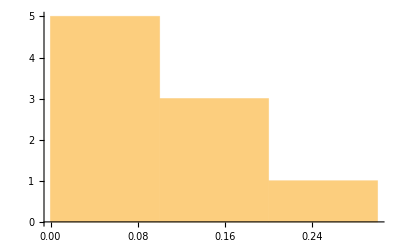

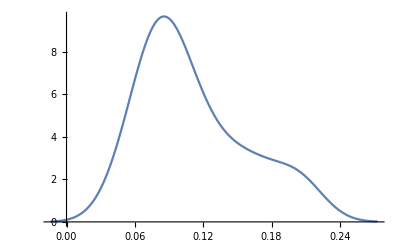

```mathematica
Histogram[markovPDF]
SmoothHistogram[markovPDF]
```

## Attractors/Repellents

Attractors

```mathematica
{attractorScaler,attractorCoverage,attractorDimension}={100,.1,2};
attractorDimensionPositions=Position[cityType,attractorDimension];
sampledAttractors=(Position[cityType,attractorDimension]//Flatten//RandomSample)[[1;;Round[attractorCoverage*Length[attractorDimensionPositions]]]]
```

{}

```mathematica
scaledInProbs=((1+attractorScaler)*migrationDimensionalMatrix[[All,#]])&/@sampledAttractors;
replacedMatrix=ReplacePart[migrationDimensionalMatrix//Transpose,(#[[1]]->#[[2]])&/@Transpose[{sampledAttractors,scaledInProbs}]]//Transpose
renormalizedMatrix=(#/Total[#])&/@replacedMatrix
MatrixPlot[Chop[migrationDimensionalMatrix-renormalizedMatrix]]
```

{{0.,0.,0.19088,0.481079,0.328041,0.,0.,0.,0.},{0.,0.,0.372872,0.254256,0.372872,0.,0.,0.,0.},{0.120343,0.303304,0.,0.,0.,0.303304,0.0559556,0.0967499,0.120343},{0.245126,0.167148,0.,0.,0.,0.0972597,0.245126,0.167148,0.0781919},{0.135143,0.19819,0.,0.,0.,0.19819,0.135143,0.19819,0.135143},{0.,0.,0.417227,0.165545,0.417227,0.,0.,0.,0.},{0.,0.,0.0988479,0.535799,0.365353,0.,0.,0.,0.},{0.,0.,0.159424,0.340794,0.499782,0.,0.,0.,0.},{0.,0.,0.283887,0.228231,0.487881,0.,0.,0.,0.}}

{{0.,0.,0.19088,0.481079,0.328041,0.,0.,0.,0.},{0.,0.,0.372872,0.254256,0.372872,0.,0.,0.,0.},{0.120343,0.303304,0.,0.,0.,0.303304,0.0559556,0.0967499,0.120343},{0.245126,0.167148,0.,0.,0.,0.0972597,0.245126,0.167148,0.0781919},{0.135143,0.19819,0.,0.,0.,0.19819,0.135143,0.19819,0.135143},{0.,0.,0.417227,0.165545,0.417227,0.,0.,0.,0.},{0.,0.,0.0988479,0.535799,0.365353,0.,0.,0.,0.},{0.,0.,0.159424,0.340794,0.499782,0.,0.,0.,0.},{0.,0.,0.283887,0.228231,0.487881,0.,0.,0.,0.}}

-Graphics-

Repellents

```mathematica
{repellentEfficacy,repellentCoverage,repellentDimension}={1,.5,1};
repellentDimensionPositions=Position[cityType,repellentDimension];
sampledRepellents=(repellentDimensionPositions//Flatten//RandomSample)[[1;;Round[repellentCoverage*Length[repellentDimensionPositions]]]]
```

{2,7,1}

## Killing

```mathematica
{killingScaler,killingCoverage,killingDimension}={100,.2,3};
killingDimensionPositions=Position[cityType,killingDimension];
sampledKilling=(Position[cityType,killingDimension]//Flatten//RandomSample)[[1;;Round[killingCoverage*Length[killingDimensionPositions]]]]
```

{}

## Random Walks

```mathematica
paths=Table[
kernel=migrationDimensionalMatrix;
initialState=ConstantArray[0,kernel//Length]//ReplacePart[#,(RandomSample[Range[kernel//Length]][[1]])->1]&;
markov=DiscreteMarkovProcess[initialState,kernel];
sim=RandomFunction[markov,{0,steps}];
path=ToString/@Part[sim["ValueList"],1];
path
,{i,1,chainsNumber}];
paths//Grid
```

Grid[{ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList,ValueList}]

## Report

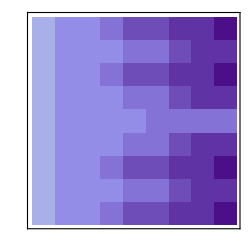
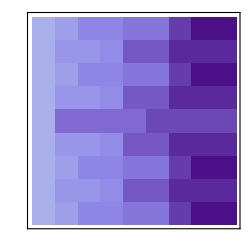
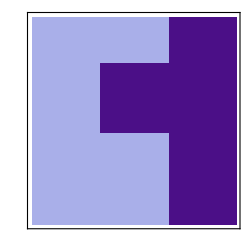
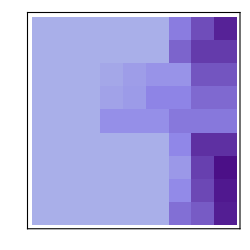
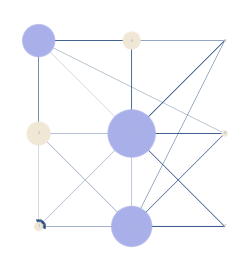
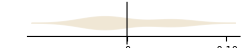
Distances Matrix | Movement Kernel | Dimensions Matrix | Applied Dimensions
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | 
Pointset | Markov Baseline | Markov Dimensional | Abs[Baseline-Dimensional]
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | 
 |  | Differences Distribution | Markov Distributions
 |  | -Graphics- | -Graphics-

Export::nodir: Directory /Users/dtcitron/Documents/MosPopDyn/MoNeT/MoNeT/Dev/DanielCitron/images/ does not exist.

Export::noopen: Cannot open ./images/002ReportGrid.png.

$Failed

```mathematica
Grid[{
Style[#,LineBreakWithin->False]&/@{"Distances Matrix","Movement Kernel","Dimensions Matrix","Applied Dimensions"},
{matrixDistancesPlot,matrixMigrationPlot,matrixPenalizationsPlot,matrixDimensionalPlot},
{"","","",""},
Style[#,LineBreakWithin->False]&/@{"Pointset","Markov Baseline","Markov Dimensional","Abs[Baseline-Dimensional]"},
{originalMap,markovBaseline,markovDimensional,markovDimensionalDifference},
{"","","",""},
Style[#,LineBreakWithin->False]&/@{"","","Differences Distribution","Markov Distributions"},
{"","",distributionOfDifferences,markovDistributions}
}]
Export["./images/"<>StringPadLeft[networkDimension//ToString,3,"0"]<>"ReportGrid.png",%,ImageSize->5000,ImageResolution->1000]
```